```mathematica
Clear["Global`*"]
```

```mathematica
IntervalRect[{min_,max_}]:=Rectangle[{min,0},{max,1}]
IntervalRect[{min_,max_},kappamax_]:=Rectangle[{min,0},{Min[max,kappamax],1}]
spectrum[list_,max_]:=Graphics[{Black,Thickness[0.0015],Line[{{#,0},{#,1}}]&/@list},PlotRange->{{0,max},{0,1}},PlotRangePadding->None,ImagePadding->{{60,30},{60,0}},ImageSize->Large,AspectRatio->1/10,Axes->None,Frame->{True,False,True,False},FrameLabel->TextCell["Laplace Matrix Eigenvalue",FontSize->14]]
spectrumIntervals[list_,max_,roots_]:=Graphics[{Lighter[Blue,0.85],IntervalRect[#,max]&/@roots,Black,Thickness[0.0015],Line[{{#,0},{#,1}}]&/@list},PlotRange->{{0,max},{0,1}},PlotRangePadding->None,ImagePadding->{{60,30},{60,0}},ImageSize->Large,AspectRatio->1/10,Axes->None,Frame->{True,False,True,False},FrameLabel->TextCell["Laplace Matrix Eigenvalue",FontSize->14]]
InverseParticipationRatio[v_]:=Norm[Normalize[v],4]^4
NormalizeMatrixRows[M_]:=Module[{A=M},
For[i=1,i≤Length[M],++i,
A[[i]]=Normalize[M[[i]],Total]
];
Return[A];
]
```

## Model functions

```mathematica
(*Define functions*)
g[i_,k_]:=x[i,k][t]^phi[[i]];
m[i_,k_]:=x[i,k][t]^mu[[i]];
Kf[i_]:=gamma[[i]]/(1-gamma[[i]]);
f[i_,k_]:=to[i,k]x[i,k][t]^psi[[i]](1+Kf[i])/(to[i,k]+Kf[i]);
to[i_,k_]:=(Sum[A[[i,j]]x[j,k][t],{j,S}])
lo[i_,j_,k_]:=x[i,k][t]^psi [[i]]x[j,k][t](1+Kf[i])/(Kf[i]+to[i,k])
e[i_,k_]:=-d[[i]]Sum[L[[k,l]]x[i,l][t],{l,Nvertices}]
```

## Parameterization

```mathematica
(* Local food web *)
S=2;
lima={{0,0},{1,0}};

(* Spatial web *)
LoadSpatialWeb6Patch[]:=Module[{},
Nvertices=6;
L={{3,-1,-1,0,0,-1},{-1,3,-1,0,-1,0},{-1,-1,2,0,0,0},{0,0,0,1,0,-1},{0,-1,0,0,1,0},{-1,0,0,-1,0,2}};
graph=KirchhoffGraph[L];
];

(* Stable for 4 species system *)
LoadSpatialWeb15Patch[]:=Module[{},
Nvertices=15;
L={{4,0,0,0,0,-1,-1,0,0,0,0,-1,0,0,-1},{0,3,0,-1,-1,0,0,0,0,-1,0,0,0,0,0},{0,0,2,0,0,0,0,-1,0,0,-1,0,0,0,0},{0,-1,0,3,-1,0,0,0,0,0,-1,0,0,0,0},{0,-1,0,-1,3,-1,0,0,0,0,0,0,0,0,0},{-1,0,0,0,-1,4,0,0,0,0,0,0,-1,0,-1},{-1,0,0,0,0,0,3,0,0,0,0,-1,0,0,-1},{0,0,-1,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,3,0,-1,0,-1,-1,0},{0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,-1,-1,0,0,0,0,-1,0,5,0,-1,-1,0},{-1,0,0,0,0,0,-1,0,0,0,0,3,0,0,-1},{0,0,0,0,0,-1,0,0,-1,0,-1,0,4,-1,0},{0,0,0,0,0,0,0,0,-1,0,-1,0,-1,3,0},{-1,0,0,0,0,-1,-1,0,0,0,0,-1,0,0,4}};
graph=KirchhoffGraph[L];
];

(*Nvertices=2;
L={{1,-1},{-1,1}};*)

(*set parameters*)
For[i=1,i≤S,++i,
(*migration rate*)
d={3,10};

(*biomass flow*)
alpha={10,3};

(*exponent parameters*)
phi={1,0};
mu={2,2};
psi={0,1};
gamma={0,0.6};

(*scale parameters*)
sigma={0.9,0};
sigmatilde=Table[1-sigma[[i]],{i,S}];

delta={0,1};
deltatilde=Table[1-delta[[i]],{i,S}];

beta=Table[If[Sum[lima[[n,i]],{n,S}]>0,lima[[j,i]]/Sum[lima[[n,i]],{n,S}],0],{j,S},{i,S}];
];

c=Table[If[lima[[i,j]]>0,1,0],{i,S},{j,S}];
A=NormalizeMatrixRows[lima];

foodweb=AdjacencyGraph[c];
top=2;
```

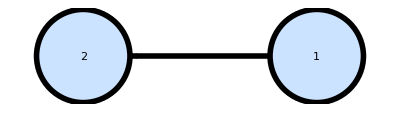

```mathematica
GraphPlot[AdjacencyGraph[c],
VertexRenderingFunction->Function[{p,l},
{RGBColor[204/255,227/255,255/255],EdgeForm[{Thickness[0.01],Black}],Disk[p,0.2],Directive[Black,FontSize->12,FontFamily->"Helvetica"],Text[l,p]}],
EdgeRenderingFunction->Function[{p,vl,el},{Black,Thickness[0.01],Arrowheads[Medium],Arrow[Reverse[p],0.2]}],
ImageSize->Automatic
]
```

```mathematica
GenerateSpatialGraphPlot[]:=Module[{thickness=0.01},
GraphPlot[KirchhoffGraph[L],
VertexRenderingFunction->Function[{p,l},{White,EdgeForm[{Thickness[thickness],RGBColor[222/255,135/255,135/255]}],Disk[p,0.25],Directive[Black,FontSize->7,FontFamily->"Helvetica"],Text[l,p]}],
EdgeRenderingFunction->Function[{p,vl,el},{RGBColor[222/255,135/255,135/255],Thickness[thickness],Line[p]}]
]
];
```

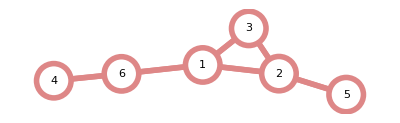

(3 | -1 | -1 | 0 | 0 | -1
-1 | 3 | -1 | 0 | -1 | 0
-1 | -1 | 2 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | -1
0 | -1 | 0 | 0 | 1 | 0
-1 | 0 | 0 | -1 | 0 | 2)

```mathematica
LoadSpatialWeb6Patch[]
GenerateSpatialGraphPlot[]
MatrixForm[L]
```

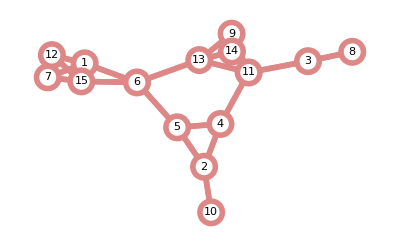

(4 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1
0 | 3 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | -1 | 0 | 3 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | -1 | 0 | -1 | 3 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | -1 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1
-1 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1
0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | -1 | 0 | -1 | -1 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 5 | 0 | -1 | -1 | 0
-1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 4 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 3 | 0
-1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 4)

```mathematica
LoadSpatialWeb15Patch[]
GenerateSpatialGraphPlot[]
MatrixForm[L]
```

## Model Equations

```mathematica
(* Homogeneous system equations right hand side *)
rhs[i_,k_]:=alpha[[i]](deltatilde[[i]]g[i,k]
+delta[[i]]If[Sum[lima[[i,j]],{j,S}]>0,f[i,k],0]
-sigmatilde[[i]]m[i,k]
-sigma[[i]]Sum[beta[[j,i]]If[beta[[j,i]]>0,lo[j,i,k],0],{j,S}])
```

```mathematica
Flatten[Table[
x[i,k]'[t]==rhs[i,k],
{i,S},{k,1}]]
```

{x[1,1]'[t]==10 (x[1,1][t]-0.1 (x[1,1][t])^2-(2.25 x[1,1][t] x[2,1][t])/(1.5+x[1,1][t])),x[2,1]'[t]==3 ((2.5 x[1,1][t] x[2,1][t])/(1.5+x[1,1][t])-(x[2,1][t])^2)}

## Jacobian

```mathematica
CalculateJacobian[]:=Module[{},
J=D[
Flatten[Table[rhs[i,k],{i,S},{k,1}]],
{Flatten[Table[x[i,k][t],{i,S},{k,1}]]}
];
J0=FullSimplify[J/.Table[x[i,1][t]->1,{i,S}]];
JM=DiagonalMatrix[Table[d[[i]],{i,S}]];
];

CalculateMSF[]:=Module[{points,dkappa=0.1},
If[!ValueQ[kappamax],kappamax=15];
CalculateJacobian[];
points=Table[{kappa,Max[Re[Eigenvalues[J0-kappa JM]]]},{kappa,-10,kappamax,dkappa}];
MSF=Interpolation[points,InterpolationOrder->1];
Return[MSF]
];

CalculateReCoMSF[]:=Module[{points,dkappa=0.01,kappa},
If[!ValueQ[kappamax],kappamax=15];
CalculateJacobian[];

RePoints={};
CoPoints={};

For[kappa=-1,kappa≤kappamax,kappa+=dkappa,
EV=First[MaximalBy[ReIm[Eigenvalues[J0-kappa JM]],First]];
If[Abs[EV[[2]]]==0,
AppendTo[RePoints,{kappa,EV[[1]]}];
,
AppendTo[CoPoints,{kappa,EV[[1]]}];
];
];
];

PlotCoReMSF[RePoints_,CoPoints_]:=Module[{},
Return[
ListPlot[
{RePoints,CoPoints},
Frame->True,
FrameLabel->{"Laplacian eigenvalue κ","Max Re Jacobian eigenvalue"},
Joined->True,
PlotRange->{{0,kappamax},Automatic}
]
];
]

PlotCoReMSF[RePoints_,CoPoints_,plotRange_]:=Module[{},
Return[
ListPlot[
{RePoints,CoPoints},
Frame->True,
FrameLabel->{"Laplacian eigenvalue κ","Max Re Jacobian eigenvalue"},
Joined->True,
PlotRange->plotRange
]
];
]

(*Find unstable interval*)
FindUnstableInterval[MSF_]:=Module[{kappa0,kappa,step=0.001,roots},
intervals={};
roots={};
If[!ValueQ[kappamax],kappamax=15];

For[kappa=0,kappa+step≤kappamax,kappa+=step,
If[MSF[kappa]MSF[kappa+step]<0,AppendTo[roots,kappa+step/2]];
];

If[Length[roots]==0,
Print["Failed to find unstable interval."];
Abort[];
];

For[i=1,i≤Length[roots],i+=2,
If[i+1≤Length[roots],
AppendTo[intervals,{roots[[i]],roots[[i+1]]}],
Print["Failed to find maximum of the last unstable interval. Set maximum to kappamax."];
AppendTo[intervals,{roots[[i]],kappamax}];
];
];

interval=First[intervals];
];
```

5

Failed to find unstable interval.

$Aborted

{}

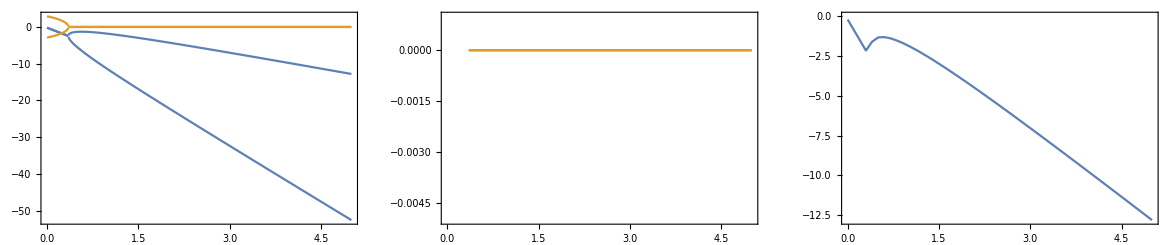

```mathematica
kappamax=5
CalculateJacobian[];
MSF=CalculateMSF[];
FindUnstableInterval[MSF];
intervals

GraphicsRow[{
Plot[{Sort[Re[Eigenvalues[J0-kappa JM]]],Sort[Im[Eigenvalues[J0-kappa JM]]]},{kappa,0,kappamax},PlotRange->Full,Frame->True,ImageSize->Medium],
Plot[{Sort[Re[Eigenvalues[J0-kappa JM]]],Sort[Im[Eigenvalues[J0-kappa JM]]]},{kappa,0,kappamax},PlotRange->{-0.005,0.001},Frame->True,ImageSize->Medium],
Plot[MSF[kappa],{kappa,0,kappamax},Frame->True,ImageSize->Medium]
}]

If[ValueQ[kappaList],spectrumIntervals[kappaList,kappamax,intervals]]
```

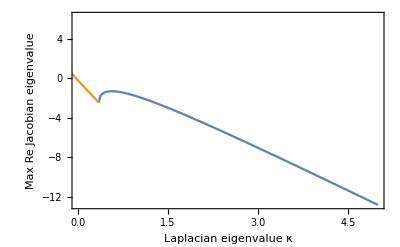

```mathematica
CalculateReCoMSF[];
MSFPlot1=PlotCoReMSF[RePoints,CoPoints]
```

## Bifurcation Diagram

```mathematica
LoadSpatialWeb15Patch[];
phi[[1]]=ϕ;
gamma[[2]]=γ;
CalculateJacobian[];
kappaList=N[Eigenvalues[L]];
J0//MatrixForm
JM//MatrixForm
```

(-2.-9. γ+10. ϕ | -9.
3 γ | -3)

(3 | 0
0 | 10)

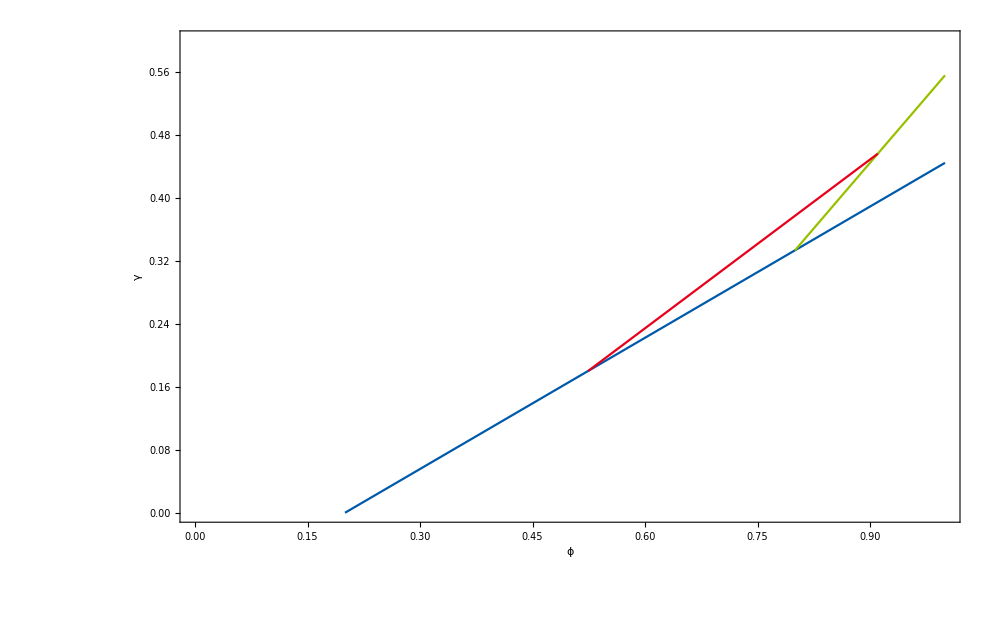

```mathematica
transkritisch=Solve[Det[J0]==0,{γ}][[1,1,2]];
hopf=Solve[Tr[J0]==0,{γ}][[1,1,2]];
turing=Solve[Det[J0-kappaList[[14]]JM]==0,{γ}][[1,1,2]];
turingList=Simplify[Table[Solve[Det[J0-kappaList [[i]]JM]==0,{γ}][[1,1,2]],{i,1,Length[kappaList]}]];

transhopf=Solve[hopf==transkritisch][[1,1,2]];
turinghopf=Solve[turing==hopf][[1,1,2]];
transturing=Solve[turing==transkritisch][[1,1,2]];

pltTranskritisch=Plot[transkritisch,{ϕ,0,1},PlotRange->{0,0.6},Frame->True,FrameLabel->{ϕ,γ},PlotStyle->RGBColor["#005AA9"],ImageSize->1000];
pltHopf=Plot[hopf,{ϕ,transhopf,1},PlotRange->{0,1},Frame->True,FrameLabel->{ϕ,γ},PlotStyle->RGBColor["#99C000"]];
pltTuring=Plot[turing,{ϕ,transturing,turinghopf},PlotRange->{0,1},Frame->True,FrameLabel->{ϕ,γ},PlotStyle->RGBColor["#E6001A"]];
pltTuringList=Plot[turingList,{ϕ,0,1},PlotRange->{0,1},Frame->True,FrameLabel->{ϕ,γ},PlotStyle->RGBColor["#E6001A"]];

Turing1[x_]:=y/.FullSimplify[Solve[alpha[[1]] d[[2]](x-sigma[[1]]y-sigmatilde[[1]]mu[[1]])+alpha[[2]] d[[1]](psi[[2]]-mu[[2]])==0,y]][[1]];
p=(alpha[[1]]/alpha[[2]])*(d[[2]]/d[[1]]);
TuringKont[x_]:=y/.FullSimplify[Solve[(p x -p y-psi[[2]]+mu[[2]])^2-4 p psi[[2]]y==0,y]][[1]];
turinghopfKont=Solve[TuringKont[ϕ]==hopf][[1,1,2]];
transturingKont=Solve[TuringKont[ϕ]==transkritisch][[1,1,2]];
pltTuring1=Plot[Turing1[ϕ],{ϕ,0,1},PlotStyle->{Dashed,RGBColor["#E6001A"]}];
pltTuringKont=Plot[TuringKont[ϕ],{ϕ,0,1},PlotRange->{0,1},Frame->True,FrameLabel->{ϕ,γ},PlotStyle->{Dashed,RGBColor["#EC6500"]}];

pltBifurcation=Show[pltTranskritisch,pltHopf,pltTuring]
pltTuring1;
```

```mathematica
parameterPicker=LocatorPane[Dynamic[{phi[[1]],gamma[[2]]}],pltBifurcation]
Dynamic[{phi[[1]],gamma[[2]]}]
```

```mathematica
Flatten[Table[rhs[i,k],{i,S},{k,1}]]//FullSimplify
```

{10 (-0.1 (x[1,1][t])^2+(x[1,1][t])^ϕ+(0.9 x[1,1][t] x[2,1][t])/(-1. γ+(-1.+γ) x[1,1][t])),3 ((x[1,1][t])/(γ-(-1+γ) x[1,1][t])-x[2,1][t]) x[2,1][t]}

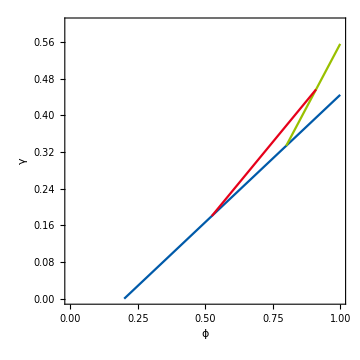

```mathematica
pltTranskritisch=Plot[transkritisch,{ϕ,0,1},PlotRange->{0,0.6},Frame->True,FrameLabel->{ϕ,γ},PlotStyle->RGBColor["#005AA9"],ImageSize->5 72,AspectRatio->1];
pltHopf=Plot[hopf,{ϕ,transhopf,1},PlotRange->{0,1},Frame->True,FrameLabel->{ϕ,γ},PlotStyle->RGBColor["#99C000"]];
pltTuring=Plot[turing,{ϕ,transturing,turinghopf},PlotRange->{0,1},Frame->True,FrameLabel->{ϕ,γ},PlotStyle->RGBColor["#E6001A"]];
pltTuringList=Plot[turingList,{ϕ,0,1},PlotRange->{0,1},Frame->True,FrameLabel->{ϕ,γ},PlotStyle->RGBColor["#E6001A"]];
pltBifurcationPaper=Show[pltTranskritisch,pltHopf,pltTuring]
```

```mathematica
transkritisch
```

0.0185185 (-6.+30. ϕ)

```mathematica
hopf
```

-0.111111 (5.-10. ϕ)

```mathematica
turing
```

0.013219 (-14.7114+54.0539 ϕ)

```mathematica
transhopf
```

0.8

```mathematica
transturing
```

0.524323

```mathematica
turinghopf
```

0.910518

## Homogeneous System

```mathematica
(*set starting conditions*)
setStartHomogen[]:=Module[{delta=0.01},
startHomogen=
Flatten[
Table[
x[i,k][0]==RandomReal[{1-delta,1+delta}],
{i,S},{k,1}]
];
];

(*Solve ODE*)
solveHomogen[Tmax_]:=Module[{sol},
setStartHomogen[];
sol=NDSolve[Join[{eqnsHomogen,startHomogen}],varsHomogen,{t,0,Tmax},MaxSteps->100000][[1]];
Return[varsHomogen/.sol];
];

EvaluateHomogenSystem[Tmax_]:=Module[{},
(*generate equations*)
eqnsHomogen=Flatten[Table[
x[i,k]'[t]==rhs[i,k],
{i,S},{k,1}]];

(*dependent variables*)
varsHomogen = Flatten[
Table[
x[i,k][t]
,{i,S},{k,1}]
];

(*solve deqns*)
solHomogen=solveHomogen[Tmax];
XSList=solHomogen/.t->Tmax;

(*set steady state values*)
For[i=1,i≤S,++i,
XS[i]=XSList[[i]];
TS[i]=Sum[c[[i,j]]XS[j],{j,S}];
];
];
```

```mathematica
phi[[1]]=0.99;
gamma[[2]]=0.525;
parameterPicker
```

## Solver

### Local

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerLocal[]:=Module[{y},
Tmax=100.;
maxsteps=100000;
dt=Tmax/maxsteps;

data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

For[i=1,i≤S,++i,
data[[1,i]]=1+RandomReal[{-0.1,0.1}];
];

For[step=1,step<maxsteps,step++,
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaLocal[noise_,tmax_,maxSteps_]:=Module[{y},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S}];
data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

For[i=1,i≤S,++i,
data[[1,i]]=1+RandomReal[{-0.1,0.1}];
];

For[step=1,step<maxsteps,step++,
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
data[[step+1]]=data[[step+1]]/.{x_?Negative->0};
];
];

EulerMaruyamaLocal[noise_]:=Module[{y},
EulerMaruyamaLocal[noise,100,100000];
];
```

### Spatial

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerSpatial[]:=Module[{y},
Tmax=500.;
maxsteps=100000;
dt=Tmax/maxsteps;

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
data[[1,i,k]]=1+RandomReal[{-0.1,0.1}];
];
];

For[step=1,step<maxsteps,step++,
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaSpatial[noise_,Tmax_,maxsteps_]:=Module[{y},
dt=Tmax/maxsteps;

(*noise=0.01;*)
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
data[[1,i,k]]=1;
];
];

For[step=1,step<maxsteps,step++,
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
data[[step+1]]=data[[step+1]]/.{x_?Negative->0};
];
];
```

```mathematica
EulerMaruyamaSpatial[noise_,Tmax_,maxsteps_,initialData_]:=Module[{y},
dt=Tmax/maxsteps;

(*noise=0.01;*)
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

data[[1]]=initialData;

For[step=1,step<maxsteps,step++,
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
data[[step+1]]=data[[step+1]]/.{x_?Negative->0};
];
];
```

### Local variable phi

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerLocalVariable[phiInterval_,gammaInterval_]:=Module[{y,phistep,phit,gammastep,gammat},
Tmax=100.;
maxsteps=100000;
dt=Tmax/maxsteps;

phistep=(phiInterval[[2]]-phiInterval[[1]])/maxsteps;
phi[[1]]=phit;
gammastep=(gammaInterval[[2]]-gammaInterval[[1]])/maxsteps;
gamma[[2]]=gammat;

data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

For[i=1,i≤S,++i,
data[[1,i]]=1+RandomReal[{-0.1,0.1}];
];

For[step=1,step<maxsteps,step++,
phit=phiInterval[[1]]+step phistep;
gammat=gammaInterval[[1]]+step gammastep;
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaLocalVariable[phiInterval_,gammaInterval_,noise_,tmax_,maxSteps_]:=Module[{y,phistep,phit,gammastep,gammat},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

phistep=(phiInterval[[2]]-phiInterval[[1]])/maxsteps;
phi[[1]]=phit;
gammastep=(gammaInterval[[2]]-gammaInterval[[1]])/maxsteps;
gamma[[2]]=gammat;

Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S}];
data=Table[0,{maxsteps},{i,S}];
eqns=Flatten[Table[rhs[i,k],{i,S},{k,1}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,1}]];

For[i=1,i≤S,++i,
data[[1,i]]=1+RandomReal[{-0.1,0.1}];
];

For[step=1,step<maxsteps,step++,
phit=phiInterval[[1]]+step phistep;
gammat=gammaInterval[[1]]+step gammastep;
k=1;
For[i=1,i≤S,++i,
y[i,k]=data[[step,i]];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
data[[step+1]]=data[[step+1]]/.{x_?Negative->0};
];
];

EulerMaruyamaLocalVariable[phiInterval_,gammaInterval_,noise_]:=Module[{y},
EulerMaruyamaLocalVariable[phiInterval,gammaInterval,noise,100,100000];
];
```

### Spatial variable phi

```mathematica
(* Euler-Verfahren *)
(* ohne Noise *)
EulerSpatialVariable[phiInterval_,gammaInterval_]:=Module[{y,phistep,phit,gammastep,gammat},
Tmax=500.;
maxsteps=100000;
dt=Tmax/maxsteps;

phistep=(phiInterval[[2]]-phiInterval[[1]])/maxsteps;
phi[[1]]=phit;
gammastep=(gammaInterval[[2]]-gammaInterval[[1]])/maxsteps;
gamma[[2]]=gammat;

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
data[[1,i,k]]=1+RandomReal[{-0.1,0.1}];
];
];

For[step=1,step<maxsteps,step++,
phit=phiInterval[[1]]+step phistep;
gammat=gammaInterval[[1]]+step gammastep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt;
];
];
```

```mathematica
(* Euler-Maruyama-Verfahren *)
(* Wiener Prozess *)
EulerMaruyamaSpatialVariable[phiInterval_,gammaInterval_,noise_,tmax_,maxSteps_]:=Module[{y,phit,phistep,gammastep,gammat},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

phistep=(phiInterval[[2]]-phiInterval[[1]])/maxsteps;
phi[[1]]=phit;
gammastep=(gammaInterval[[2]]-gammaInterval[[1]])/maxsteps;
gamma[[2]]=gammat;

(*noise=0.01;*)
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
data[[1,i,k]]=1+RandomReal[{-0.1,0.1}];
];
];

For[step=1,step<maxsteps,step++,
phit=phiInterval[[1]]+step phistep;
gammat=gammaInterval[[1]]+step gammastep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
data[[step+1]]=data[[step+1]]/.{x_?Negative->0};
];
];

EulerMaruyamaSpatialVariable[phiInterval_,gammaInterval_,noise_]:=Module[{y},
EulerMaruyamaSpatialVariable[phiInterval,gammaInterval,noise,100,100000];
];

EulerMaruyamaSpatialVariable[phiInterval_,gammaInterval_,noise_,tmax_,maxSteps_,initialData_]:=Module[{y,phit,phistep,gammastep,gammat},
Tmax=tmax;
maxsteps=maxSteps;
dt=Tmax/maxsteps;

phistep=(phiInterval[[2]]-phiInterval[[1]])/maxsteps;
phi[[1]]=phit;
gammastep=(gammaInterval[[2]]-gammaInterval[[1]])/maxsteps;
gamma[[2]]=gammat;

(*noise=0.01;*)
Noise[]:=Table[RandomVariate[NormalDistribution[0,Sqrt[dt]]],{S},{Nvertices}];

data=Table[0,{maxsteps},{i,S},{k,Nvertices}];
eqns=FullSimplify[Table[rhs[i,k]+e[i,k],{i,S},{k,Nvertices}]]/.Flatten[Table[(x[i,k][t])->y[i,k],{i,S},{k,Nvertices}]];

data[[1]]=initialData;

For[step=1,step<maxsteps,step++,
phit=phiInterval[[1]]+step phistep;
gammat=gammaInterval[[1]]+step gammastep;
For[i=1,i≤S,++i,
For[k=1,k≤Nvertices,++k,
y[i,k]=data[[step,i,k]];
];
];
data[[step+1]]=data[[step]]+eqns dt+noise Sqrt[data[[step]]]Noise[];
data[[step+1]]=data[[step+1]]/.{x_?Negative->0};
];
];
```